```mathematica
(* Ravnovesna lega *)
a=FullSimplify[Solve[0==m g -k(d0+x),x][[1]][[1]][[2]]]
pop=FullSimplify[Solve[0==m g + (c A^2)/(4 x0^2 (1+(ω R c)^2))-k(d0+x),x][[1]][[1]][[2]]]
pop=pop-a
```

-d0+(g m)/k

-d0+(g m)/k+(A^2 c)/(4 x0^2 (k+c^2 k R^2 ω^2))

(A^2 c)/(4 x0^2 (k+c^2 k R^2 ω^2))

```mathematica
(* Diferencialna enačba za nihanje *)
 x''[t]+ω0^2 x[t]==(c A^2)/(2 x0^2 m(1+(ω R c)^2))Sin[ω t -δ]^2
FullSimplify[DSolve[%,x[t],t][[1,1,2]]]
```

ω0^2 x[t]+x''[t]==(A^2 c Sin[δ-t ω]^2)/(2 m x0^2 (1+c^2 R^2 ω^2))

(A^2 c (4 ω^2-ω0^2+ω0^2 Cos[2 (δ-t ω)]))/(4 m x0^2 (1+c^2 R^2 ω^2) ω0^2 (4 ω^2-ω0^2))+C[1] Cos[t ω0]+C[2] Sin[t ω0]

```mathematica
(* Diferencialna enačba za nihanje razvita okrog ravnovesne lege *) 
x''[t]+ω0^2 x[t]==-(c A^2)/(4 x0^2 m(1+(ω R c)^2))Cos[2(ω t -δ)]
s1=FullSimplify[DSolve[%,x[t],t][[1,1,2]]]
```

ω0^2 x[t]+x''[t]==-(A^2 c Cos[2 (-δ+t ω)])/(4 m x0^2 (1+c^2 R^2 ω^2))

(A^2 c Cos[2 (δ-t ω)])/(4 m x0^2 (1+c^2 R^2 ω^2) (4 ω^2-ω0^2))+C[1] Cos[t ω0]+C[2] Sin[t ω0]

```mathematica
(* Izračun z izbranimi začetnimi pogoji za risanje grafov (spodnja enačba je za resonanco) *)
{ x''[t]+ω0^2 x[t]==(c A^2)/(2 x0^2 m(1+(ω R c)^2))Sin[ω t -δ]^2,x[0]==x0,x'[0]==0};
sol=FullSimplify[DSolve[%,x[t],t][[1,1,2]]];
 {x''[t]+4 ω^2 x[t]==(c A^2)/(2 x0^2 m(1+(ω R c)^2))Sin[ω t -δ]^2,x[0]==x0,x'[0]==0};
res=FullSimplify[DSolve[%,x[t],t][[1,1,2]]];
```

```mathematica
(* Časovna odvisnost izven resonance v odvisnosti od vzbujevalne frekvence *)
pogoji=
{δ->ArcTan[ω ],ω0->Pi,m->0.1,A->10,c->1,R->1,x0->1};
sol/.pogoji;
Manipulate [Plot[%,{t,0,10}],{ω,0.01Pi,5Pi}]
```

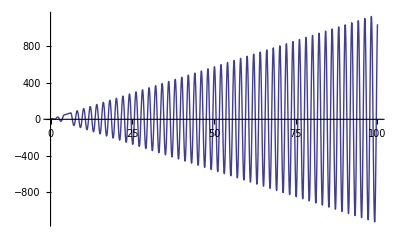

```mathematica
(* Časovna odvisnost resonance *)
res/.pogoji/.ω->.5Pi;
Plot[%,{t,0,100}]
```